```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"];
```

```mathematica
(*Calculations for capture in White Dwarf*)
```

```mathematica
Mpl=1.2211*10^19;(*in GeV*)
vesc=6*10^6;(*in m/sec*)
vbar=20.0*10^3;(*in m/sec*)
G=6.67*10^-11;(*in SI*)
ρ=10^10;(*in kg/m^3*)
clight=3 10^8(*m/sec*);
ρx=10^6*100;(*in GeV/m^3*)(*Due to Overdensity*)
mn=12.0;(*in GeV*)
tage=3 10^17(*Age in sec*);
n=10^36(*in m^-3*);
rstar=6 10^6(*in m*);
Nn=4/3 π rstar^3 n;
sigmasat=(π rstar^2)/Nn;
Msun=2 10^30(*Kg, Solar mass*);
```

```mathematica
βplus[mx_?NumericQ]:=(4 mn  mx)/(mn+mx)^2;
mr[mx_?NumericQ]:=(mn  mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*(vesc/clight);
hbar=(6.626 10^-34)/(2 π);
pf=hbar (3 π^2 n)^(1/3);
kb=1.38*10^-23(*in J/k*);
```

```mathematica
rth[mx_,T_]:=((9 kb T)/(4 π G ρ mx 1.78 10^-27))^0.5;
vth[mx_,T_]:=4/3 π rth[mx,T]^3;
A=12;mp=1.0;
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
mup[mx_?NumericQ]:=(mp *mx)/(mp+mx);
fMBboosted[u_]:=(3/(2 vbar^2))^(3/2)4/(√π)u^2 Exp[-3/(2 vbar^2)u^2](*Exp[-η^2] Sinh[2 (√(3/(2 vbar^2))u) η]/(2(√(3/(2 vbar^2))u) η)*) ;  
g1[u_?NumericQ,mx_?NumericQ,mphi_?NumericQ]:=(vesc^2-u^2)/(vesc^2+u^2)(1+mx^2/mphi^2((u^2+vesc^2)/clight^2))/((1+mx^2/mphi^2(u/clight)^2)(1+mx^2/mphi^2(vesc/clight)^2));
y=vesc/vbar;
Cself[sigmaSelf_,mx_]:=If[y≤ 100,1/3 √(6/π)ρx/mx sigmaSelf vbar(3 y^2+2Exp[-3/2 y^2]-2),1/3 √(6/π)ρx/mx sigmaSelf vbar(3 y^2-2)]
Cselfgeneral[sigmaSelf_,mx_,mphi_]:=sigmaSelf ρx/mx NIntegrate[fMBboosted[u]/u(u^2+vesc^2)(g1[u,mx,mphi]),{u,0,vesc}]
```

```mathematica
asq[mx_]:=3/2 vesc^2/vbar^2(4 mx mn)/(mx-mn)^2;
C0[mx_,sigma_]:=If[asq[mx]≤ 100,
(ρx/mx(6/π)^0.5 Min[A^2*mr[mx]^2/mup[mx]^2*sigma,sigmasat] Min[1,δp[mx]/pf]vbar Nn vesc^2/vbar^2(1-(1-Exp[-asq[mx]])/asq[mx])),
(ρx/mx(6/π)^0.5 Min[A^2*mr[mx]^2/mup[mx]^2*sigma,sigmasat] Min[1,δp[mx]/pf]vbar Nn vesc^2/vbar^2(1-1/asq[mx]))];(*With nucleon*)
```

```mathematica
Cann[sigmaAnn_,mx_,T_]:=sigmaAnn/vth[mx,T];
```

```mathematica
tsat[sigma_,sigmaSelf_?NumericQ,mx_?NumericQ,T_]:=1/Cself[sigmaSelf,mx] Log[(π (rth[mx,T])^2)/sigmaSelf Cself[sigmaSelf,mx]/C0[mx,sigma]+1.]
t1[sigma_?NumericQ,mx_?NumericQ,Mstar_,R_]:=3 10^3(10^-44/sigma)(mx/10^6)((1.4Msun)/Mstar)^(3/2)(R/(2.5 10^6))^(7/2)(12.0 4/(mx βplus[mx]))(*in secs, checked!*)
tTherm[mx_,sigma_,T_]:=(mx^2(vesc/clight) mn)/(6 T n sigma (mr[mx])^2)1/(3 10^8 8.62 10^-14)(*in secs, checked!*)
```

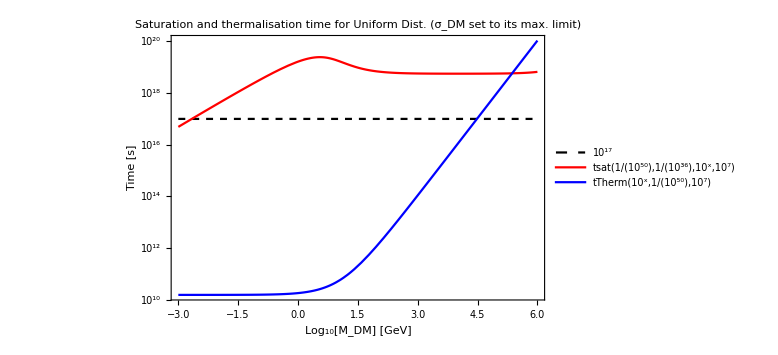

```mathematica
LogPlot[{10^17,tsat[10^-50,10^-36,10^x,10^7],tTherm[10^x,10^-50,10^7]},{x,-3,6},ImageSize->Large, Frame->True,FrameStyle->Directive[14,"Times",Black],AxesOrigin->{-3,0},PlotLegends->"Expressions",PlotStyle->{{Thick,Dashed,Black},Red,Blue},FrameLabel->{"Log_10[M_DM] [GeV]","Time [s]"},PlotLabel->"Saturation and thermalisation time for Uniform Dist. (σ_DM set to its max. limit)"]
```

```mathematica
Rstar[mx_?NumericQ,sigma_?NumericQ,t_?NumericQ]:=If[t≥t1[sigma,mx,Msun,rstar],rstar(1+(8π mr[mx]^2 n^2 sigma G rstar^2(t-t1[sigma,mx,Msun,rstar]))/(3 mx (vesc/clight))(1.78/3 10^-35))^(-1/2),rstar]
```

```mathematica
Xi[mx_?NumericQ,sigma_?NumericQ,sigmaSelf_?NumericQ,sigmaAnn_?NumericQ,T_]:=1/(√(C0[mx,sigma]Cann[sigmaAnn,mx,T]+Cself[sigmaSelf,mx]^2/4));
```

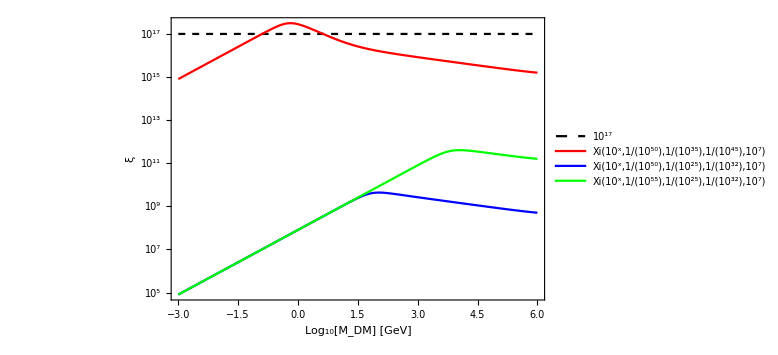

```mathematica
LogPlot[{10^17,Xi[10^x,10^-50,10^-35,10^-45,10^7],Xi[10^x,10^-50,10^-25,10^-32,10^7],Xi[10^x,10^-55,10^-25,10^-32,10^7]},{x,-3,6},ImageSize->Large, Frame->True,FrameStyle->Directive[14,"Times",Black],AxesOrigin->{-3,0},PlotLegends->"Expressions",PlotStyle->{{Thick,Dashed,Black},Red,Blue,Green},FrameLabel->{"Log_10[M_DM] [GeV]","ξ"}]
```

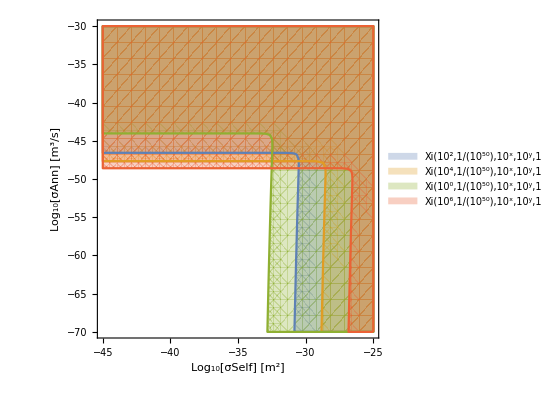

```mathematica
RegionPlot[{Xi[10^2,10^-50,10^x,10^y,10^7]≤10^17,Xi[10^4,10^-50,10^x,10^y,10^7]≤10^17,Xi[10^0,10^-50,10^x,10^y,10^7]≤10^17,Xi[10^6,10^-50,10^x,10^y,10^7]≤10^17},{x,-25,-45},{y,-30,-70},PlotLegends->"Expressions",FrameLabel->{"Log_10[σSelf] [m^2]","Log_10[σAnn] [m^3/s]"}]//Quiet
```

```mathematica
Eta[mx_,sigma_]:=(8π mr[mx]^2 n^2 sigma G rstar^2)/(3mx (vesc/clight))(1.78/3 10^-35);
```

```mathematica
Tanh[0.]
```

0.

```mathematica
Ntot[mx_?NumericQ,sigma_?NumericQ,sigmaSelf_?NumericQ,sigmaAnn_?NumericQ,T_?NumericQ,t_?NumericQ]:=(C0[mx,sigma]Tanh[t/Xi[mx,sigma,sigmaSelf,sigmaAnn,T]])/((Xi[mx,sigma,sigmaSelf,sigmaAnn,T])^-1-0.5Cself[sigmaSelf,mx]Tanh[t/Xi[mx,sigma,sigmaSelf,sigmaAnn,T]])
```

```mathematica
solveTsat[mx_?NumericQ,sigma_?NumericQ,sigmaSelf_?NumericQ,sigmaAnn_?NumericQ,T_]:=tnew/.FindRoot[π Rstar[mx,sigma,tnew]^2==sigmaSelf Ntot[mx,sigma,sigmaSelf,sigmaAnn,T,tnew],{tnew,10^20}];
```

```mathematica
solveTsat[10^-4,10^-50,10^-42,10^-32,10^7]
```

3.7569×10^24

```mathematica
tsatNEW[mx_?NumericQ,sigma_?NumericQ,sigmaSelf_?NumericQ,sigmaAnn_?NumericQ,T_]:=1/Eta[mx,sigma]((π rstar^2((Xi[mx,sigma,sigmaSelf,sigmaAnn,T])^-1-0.5Cself[sigmaSelf,mx]))/(C0[mx,sigma]sigmaSelf)+Eta[mx,sigma]t1[sigma,mx,Msun,rstar]-1)
```

```mathematica
tsatAfterTh[mx_?NumericQ,sigma_?NumericQ,sigmaSelf_?NumericQ,sigmaAnn_?NumericQ,T_]:=Xi[mx,sigma,sigmaSelf,sigmaAnn,T]ArcTanh[(π rth[mx,T]^2(Xi[mx,sigma,sigmaSelf,sigmaAnn,T])^-1)/(C0 [mx,sigma]sigmaSelf+0.5Cself[sigmaSelf,mx]π rth[mx,T]^2)]
```

```mathematica
teq[mx_?NumericQ,sigma_?NumericQ,sigmaSelf_?NumericQ,sigmaAnn_?NumericQ,T_]:=Xi[mx,sigma,sigmaSelf,sigmaAnn,T];
```

```mathematica
tsatNEW[10^1,10^-50,10^-42,10^-32,10^7]
```

3.30606×10^25

```mathematica
tsatAfterTh[10^5,10^-50,10^-42,0,10^7]
```

5.69273×10^24

```mathematica
tsat[10^-50,10^-42,10^5,10^7]
```

5.69273×10^24

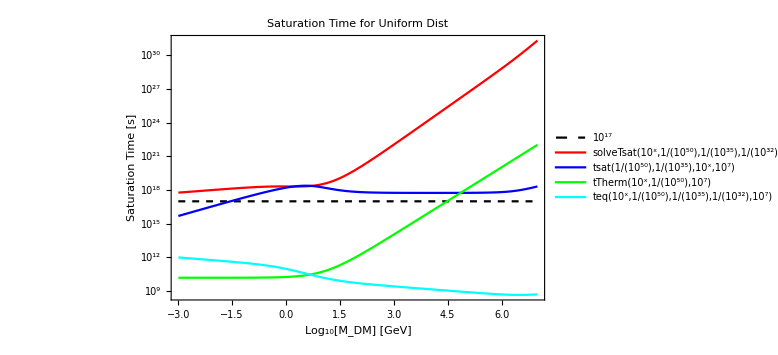

```mathematica
LogPlot[{10^17,solveTsat[10^x,10^-50,10^-35,10^-32,10^7],tsat[10^-50,10^-35,10^x,10^7],tTherm[10^x,10^-50,10^7],teq[10^x,10^-50,10^-35,10^-32,10^7]},{x,-3,7},ImageSize->Large, Frame->True,FrameStyle->Directive[14,"Times",Black],AxesOrigin->{-3,0},PlotLegends->"Expressions",PlotRange->Full,PlotStyle->{{Thick,Dashed,Black},Red,Blue,Green,Cyan},FrameLabel->{"Log_10[M_DM] [GeV]","Saturation Time [s]"},PlotLabel->"Saturation Time for Uniform Dist"]
```

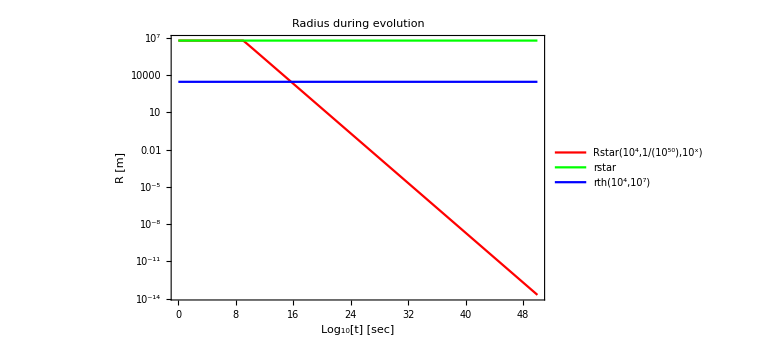

```mathematica
LogPlot[{Rstar[10^4,10^-50,10^x],rstar,rth[10^4,10^7]},{x,0,50},ImageSize->Large, Frame->True,FrameStyle->Directive[14,"Times",Black],AxesOrigin->{0,0},PlotLegends->"Expressions",PlotStyle->{Red,Green,Blue,Cyan},FrameLabel->{"Log_10[t] [sec]","R [m]"},PlotLabel->"Radius during evolution"]
```

```mathematica
tsatFinal[mx_,sigma_,sigmaSelf_,sigmaAnn_,T_]:=If[tsat[sigma,sigmaSelf,mx,T]>tTherm[mx,sigma,T],tsat[sigma,sigmaSelf,mx,T],tsatNEW[mx,sigma,sigmaSelf,sigmaAnn,T],tsat[sigma,sigmaSelf,mx,T]]
```

```mathematica
tsatFinal[10^3,10^-50,10^-30,10^-32,10^7]
```

1.11834×10^17

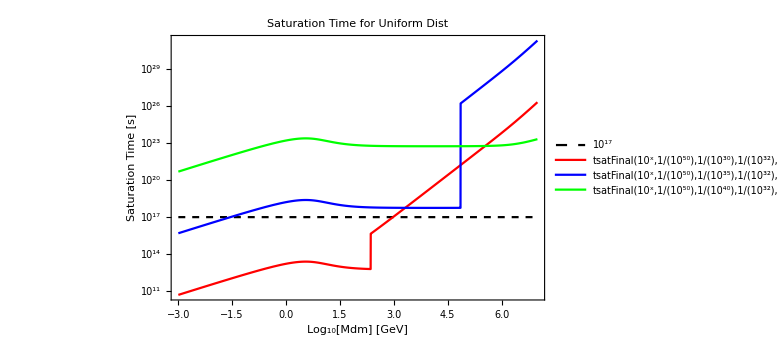

```mathematica
LogPlot[{10^17,tsatFinal[10^x,10^-50,10^-30,10^-32,10^7],tsatFinal[10^x,10^-50,10^-35,10^-32,10^7],tsatFinal[10^x,10^-50,10^-40,10^-32,10^7]},{x,-3,7},ImageSize->Large, Frame->True,FrameStyle->Directive[14,"Times",Black],AxesOrigin->{-3,0},PlotLegends->"Expressions",PlotStyle->{{Thick,Dashed,Black},Red,Blue,Green},PlotRange-> Full,FrameLabel->{"Log_10[Mdm] [GeV]","Saturation Time [s]"},PlotLabel->"Saturation Time for Uniform Dist"]
```

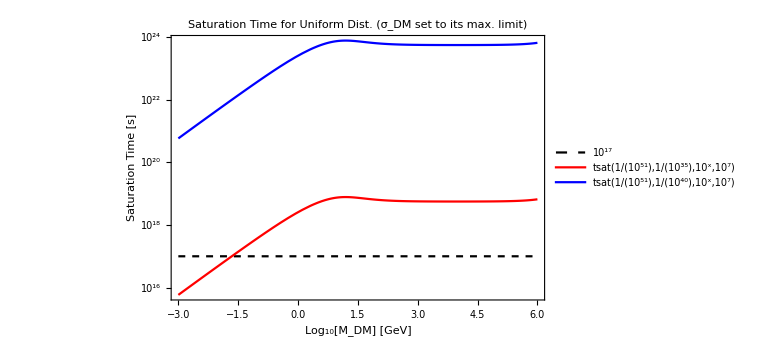

```mathematica
LogPlot[{10^17,tsat[10^-51,10^-35,10^x,10^7],tsat[10^-51,10^-40,10^x,10^7]},{x,-3,6},ImageSize->Large, Frame->True,FrameStyle->Directive[14,"Times",Black],AxesOrigin->{-3,0},PlotLegends->"Expressions",PlotStyle->{{Thick,Dashed,Black},Red,Blue},FrameLabel->{"Log_10[M_DM] [GeV]","Saturation Time [s]"},PlotLabel->"Saturation Time for Uniform Dist. (σ_DM set to its max. limit)"]
```

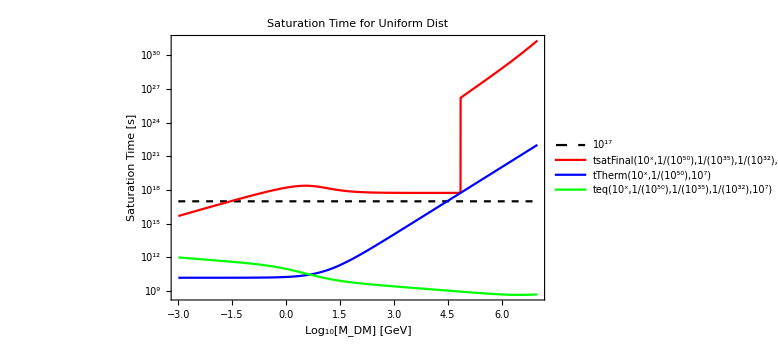

```mathematica
LogPlot[{10^17,tsatFinal[10^x,10^-50,10^-35,10^-32,10^7],tTherm[10^x,10^-50,10^7],teq[10^x,10^-50,10^-35,10^-32,10^7]},{x,-3,7},ImageSize->Large, Frame->True,FrameStyle->Directive[14,"Times",Black],AxesOrigin->{-3,0},PlotLegends->"Expressions",PlotRange->Full,PlotStyle->{{Thick,Dashed,Black},Red,Blue,Green,Cyan},FrameLabel->{"Log_10[M_DM] [GeV]","Saturation Time [s]"},PlotLabel->"Saturation Time for Uniform Dist"]
```

```mathematica
(*tsatGen[sigma_?NumericQ,sigmaSelf_?NumericQ,mx_?NumericQ,mphi_,T_]:=1/Cselfgeneral[sigmaSelf,mx,mphi] Log[(π (rth[mx,T])^2)/sigmaSelf Cselfgeneral[sigmaSelf,mx,mphi]/C0[mx,sigma]+1.]*)
```

```mathematica
(*LogPlot[{10^17,tsatGen[10^-51,10^x/(5 10^27),10^x,0.01,10^7]},{x,-3,7},ImageSize->Large, Frame->True,FrameStyle->Directive[14,"Times",Black],AxesOrigin->{-3,0},PlotLegends->"Expressions",PlotStyle->{{Thick,Dashed,Black},Red,Green,Blue,Orange},FrameLabel->{"Log_10[M_DM] [GeV]","Saturation Time [s]"},PlotLabel->"Saturation Time for Gen. Dist. (σ_DM set to its max. limit)"]*)
```

```mathematica
Nfinal[sigma_,sigmaSelf_?NumericQ,mx_?NumericQ,T_]:=If[tsat[sigma,sigmaSelf,mx,T]≤tage,If[Cself[sigmaSelf,mx]tsat[sigma,sigmaSelf,mx,T]≥10^-5,C0[mx,sigma]/Cself[sigmaSelf,mx](Exp[Cself[sigmaSelf,mx]tsat[sigma,sigmaSelf,mx,T]]-1),C0[mx,sigma]tsat[sigma,sigmaSelf,mx,T]]+(C0[mx,sigma]+π rth[mx,T]^2(1/3 √(6/π)ρx/mx vbar(3 y^2(*+2Exp[-3/2 y^2]*)-2)))(tage-tsat[sigma,sigmaSelf,mx,T]),If[Cself[sigmaSelf,mx]tage≥10^-5,C0[mx,sigma]/Cself[sigmaSelf,mx](Exp[Cself[sigmaSelf,mx]tage]-1),C0[mx,sigma]tage]]
```

```mathematica
(*NchBoson[mx_]:=1.5 10^34(100/mx)^2(*GeV*)*)
NchBoson[mx_,sigmaSelf_]:=2/π Mpl^2/mx^2(1+Mpl^2/(4 π^0.5 mx) 5.06 10^15 sigmaSelf^0.5)^0.5;(*conversion from GeV to m^-1*)
NchFermion[mx_]:=1.8 10^51(100/mx)^3(*GeV*)
Nself[mx_,T_]:=4/3 π rth[mx,T]^3 ρ/mx 1/(1.8 10^-27)
```

```mathematica
Nself[10^-2,10^7]
```

5.5894×10^58

```mathematica
Nfinal[10^-51,10^-27/5.6 10^2,10^2,10^7]
```

1.33375×10^43

```mathematica
NchBoson[10^6,10^-32]
```

3.09665×10^41

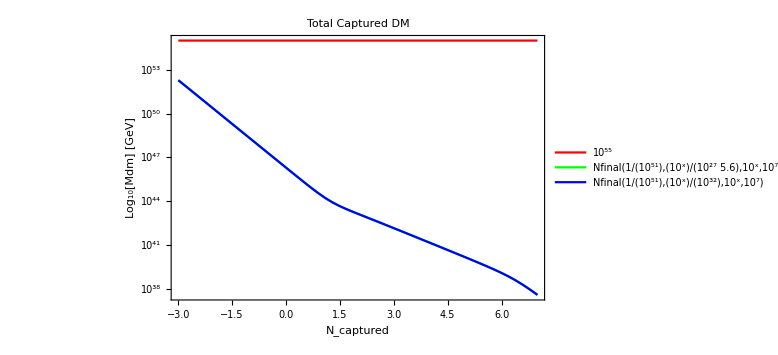

```mathematica
LogPlot[{10^55,Nfinal[10^-51,10^-27/5.6 10^x,10^x,10^7],Nfinal[10^-51,10^-32 10^x,10^x,10^7]},{x,-3,7},ImageSize->Large, Frame->True,FrameStyle->Directive[14,"Times",Black],AxesOrigin->{-3,0},PlotLegends->"Expressions",PlotStyle->{Red,Green,Blue},FrameLabel->{"N_captured","Log_10[Mdm] [GeV]"},PlotLabel->"Total Captured DM"]
```

```mathematica
(*cntrplot1=ContourPlot[{Nfinal[10^-51,10^x,10^mdm,10^7]==Max[NchBoson[10^mdm,10^x],Nself[10^mdm,10^7]],10^x/10^mdm==10^-28},{mdm,-2,6},{x,-20,-110},PlotLegends->Automatic,ContourLabels->All,Frame->True,FrameStyle->Directive[14,"Times",Black],FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["Log_10[σ_self] [m^2]",FontSize->20,Bold]},ImageSize -> Large,PlotLabel->Style["T_core=10^7K",FontSize->8,Bold],GridLines->Automatic,ContourStyle->{{Thick,Blue},{Thick,Red},{Thick,Dashed,Black}}]*)
```

```mathematica
Nfinal[10^-51,10^-60,10^6,10^7]
```

1.18435×10^39

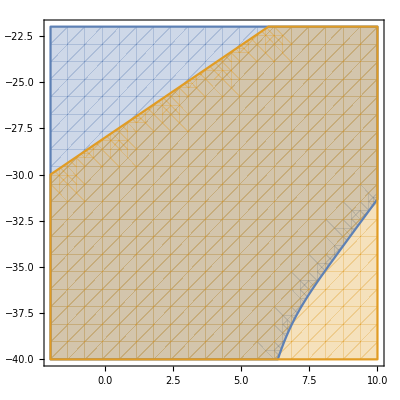

```mathematica
RegionPlot[{Nfinal[10^-51,10^x,10^mdm,10^7]≤Max[NchBoson[10^mdm,10^x],Nself[10^mdm,10^7]],10^x/10^mdm≤10^-28},{mdm,-2,10},{x,-22,-40}]
```

```mathematica
NfinalGen[sigma_,sigmaSelf_?NumericQ,mx_?NumericQ,mphi_,T_]:=(π (rth[mx,T])^2)/sigmaSelf+(C0[mx,sigma]+π rth[mx,T]^2(1/3 √(6/π)ρx/mx vbar(3 y^2(*+2Exp[-3/2 y^2]*)-2)))(tage-tsatGen[sigma,sigmaSelf,mx,mphi,T])
```

```mathematica
(*cntrplot2=ContourPlot[{NfinalGen[10^-51,10^x,10^mdm,10.,10^7]==Max[NchBoson[10^mdm,10^x],Nself[10^mdm,10^7]],10^x/10^mdm==10^-28},{mdm,-2,8},{x,-22,-40},PlotLegends->Automatic,ContourLabels->All,Frame->True,FrameStyle->Directive[14,"Times",Black],FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["Log_10[σ_self] [m^2]",FontSize->20,Bold]},ImageSize -> Large,PlotLabel->Style["T_core=10^7K, M_med=1 MeV",FontSize->8,Bold],GridLines->Automatic,ContourStyle->{{Thick,Blue},{Thick,Red},{Thick,Dashed,Black}}]*)
```

```mathematica
Qdiff=1.6 10^25 (ρ/(10^12(*kg/m^3*)))^(4/15)(*GeV s^-1*);
```

```mathematica
NsgEtrans[mx_,T_]:=1/5 π ρ G (4/3 π rth[mx,T]^3 ρ)rth[mx,T]^2(5.62 10^26)/clight^2
```

```mathematica
delT[mx_,sigmaSelf_,T_]:=(4/3 π rth[mx,T]^3)/(Nfinal[sigmaSelf,mx,T]sigmaSelf √(T/mx))
delTGen[mx_,mphi_,sigmaSelf_,T_]:=(4/3 π rth[mx,T]^3)/(NfinalGen[sigmaSelf,mx,mphi,T]sigmaSelf √(T/mx))
```

```mathematica
QDM[mx_,sigmaSelf_,T_]:=NsgEtrans[mx,T]/delT[mx,sigmaSelf,T]
QDMGen[mx_,mphi_,sigmaSelf_,T_]:=NsgEtrans[mx,T]/delTGen[mx,mphi,sigmaSelf,T]
```

```mathematica
(*cntrplot3=ContourPlot[{QDM[10^mdm,(10^x)( 10^mdm)( 1.8 10^-28),10^7]==Qdiff,x==0},{mdm,-2,6},{x,-10,5},PlotLegends->Automatic,ContourLabels->All,Frame->True,FrameStyle->Directive[14,"Times",Black],FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["Log_10[σ_self/M_DM] [cm^2 gm^-1]",FontSize->20,Bold]},ImageSize -> Large,PlotLabel->Style["T_core=10^7K",FontSize->8,Bold],GridLines->Automatic,ContourStyle->{{Thick,Blue},{Thick,Red},{Thick,Dashed,Black}}]*)
```

```mathematica
(*cntrplot4=ContourPlot[{QDMGen[10^mdm,10^-3,(10^x)( 10^mdm)( 1.8 10^-28),10^7]==Qdiff,x==0},{mdm,-2,6},{x,-10,5},PlotLegends->Automatic,ContourLabels->All,Frame->True,FrameStyle->Directive[14,"Times",Black],FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["Log_10[σ_self/M_DM] [cm^2 gm^-1]",FontSize->20,Bold]},ImageSize -> Large,PlotLabel->Style["T_core=10^7K",FontSize->8,Bold],GridLines->Automatic,ContourStyle->{{Thick,Blue},{Thick,Red},{Thick,Dashed,Black}}]*)
```

```mathematica
(*sigma corresponds to DM-carbon nuclei cross section*)
teq[mx_,sigma_,sigmaSelf_,T_,anncross_]:=2/((Cself[sigmaSelf,mx]^2+4*C0[mx,sigma]*anncross/vth[mx,T])^0.5);
```

```mathematica
teq[100.,10^-46,10^-32,10^7,10^-32]
```

3.36286×10^-41

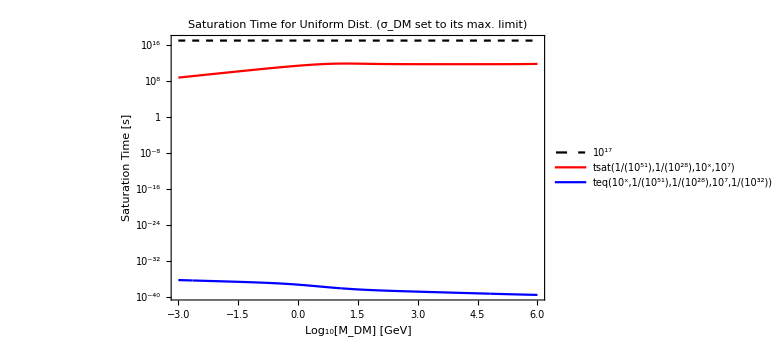

```mathematica
LogPlot[{10^17,tsat[10^-51,10^-28,10^x,10^7],teq[10^x,10^-51,10^-28,10^7,10^-32]},{x,-3,6},ImageSize->Large, Frame->True,FrameStyle->Directive[14,"Times",Black],AxesOrigin->{-3,0},PlotLegends->"Expressions",PlotStyle->{{Thick,Dashed,Black},Red,Blue},FrameLabel->{"Log_10[M_DM] [GeV]","Saturation Time [s]"},PlotLabel->"Saturation Time for Uniform Dist. (σ_DM set to its max. limit)"]
```

```mathematica
LDM[mx_?NumericQ,sigma_?NumericQ,sigmaSelf_?NumericQ,sigmaAnn_?NumericQ,T_?NumericQ]:=mx(Cann[sigmaAnn,mx,T](Ntot[mx,sigma,sigmaSelf,sigmaAnn,T,tage])^2)
```

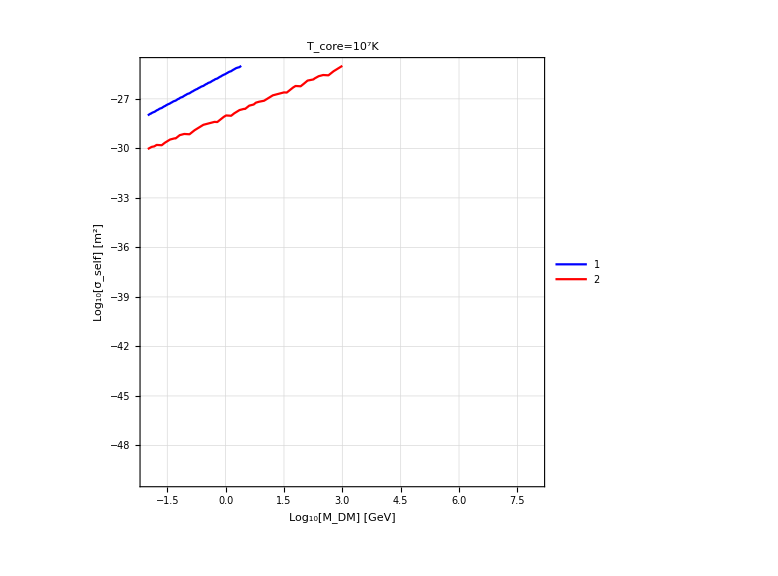

```mathematica
cntrplot3=ContourPlot[{LDM[10^mdm,10^-51,10^x,10^-32,10^5]==7 10^29,10^x/10^mdm==10^-28},{mdm,-2,8},{x,-25,-50},PlotLegends->Automatic,ContourLabels->All,Frame->True,FrameStyle->Directive[14,"Times",Black],FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["Log_10[σ_self] [m^2]",FontSize->20,Bold]},ImageSize -> Large,PlotLabel->Style["T_core=10^7K",FontSize->8,Bold],GridLines->Automatic,ContourStyle->{{Thick,Blue},{Thick,Red},{Thick,Dashed,Black}}]
```

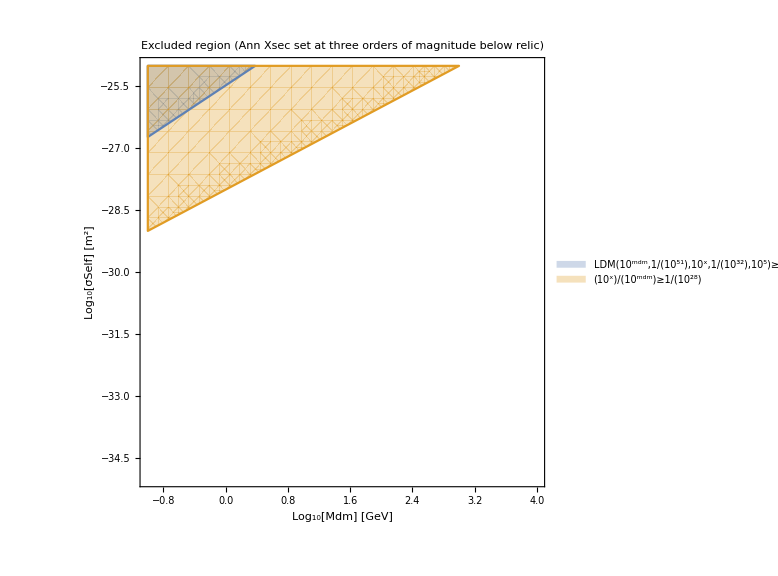

```mathematica
R1=RegionPlot[{LDM[10^mdm,10^-51,10^x,10^-32,10^5]≥7 10^29,10^x/10^mdm≥10^-28},{mdm,-1,4},{x,-25,-35},PlotLegends->"Expressions",FrameLabel->{"Log_10[Mdm] [GeV]","Log_10[σSelf] [m^2]"},PlotLabel->"Excluded region (Ann Xsec set at three orders of magnitude below relic)",ImageSize->Large]
```

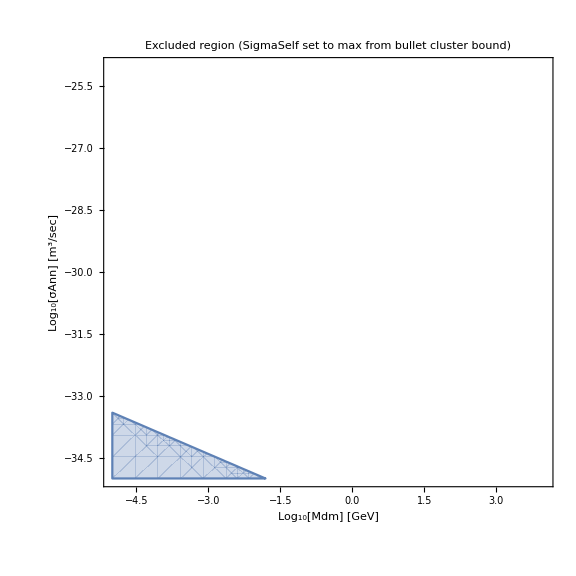

```mathematica
R2=RegionPlot[{LDM[10^mdm,10^-51,10^mdm 10^-28,10^x,10^7]≥5 10^31},{mdm,-5,4},{x,-25,-35},PlotLegends->"Expressions",FrameLabel->{"Log_10[Mdm] [GeV]","Log_10[σAnn] [m^3/sec]"},PlotLabel->"Excluded region (SigmaSelf set to max from bullet cluster bound)",ImageSize->Large]
```